```mathematica
cow=ExampleData[{"Geometry3D","Cow"}];
Manipulate[cow/. GraphicsComplex[array1_,rest___]:>GraphicsComplex[(# (Norm[#]^-coeff))&/@array1,rest],{{coeff,.25},0,1}]
```

93 :Nùmero de datos usados

FittedModel[…]

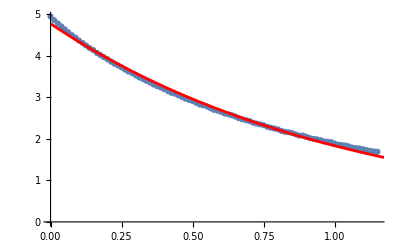

```mathematica
datos = Import["/home/taller/Documentos/Semestre 2024-2/Capacitor/Datos/Serie grupal/medidas_grupales_serie_44Mohm/datos_grupales_12.8nF_2.txt", "Data"];
datos= datos[[83;;175]];
datos = Block[{t=datos[[All,1]],v=datos[[All,2]],shift},shift= 0.956;Transpose[{t - shift,v}]];
":Nùmero de datos usados" Length[datos]

model = k E ^(c t);
ajustado = NonlinearModelFit[datos, model, {k, c}, t]
Show[ListPlot [datos], Plot[ajustado[t], {t, 0, 1.2}, PlotStyle->Red]]
```